```mathematica
RiemannBar[box:{{x0_,x1_},{y0_,y1_}},{x_,y_},_]:=Block[{area=N@(y1+y0) (x1-x0)},Sow[area];
{(*ChartElementData["Rectangle"][box,{},{}],*)
{Opacity[0.5],Blue,EdgeForm[Thickness[Medium]],Rectangle[{x0,y0},{x1,y1}]},
{Opacity[1],Black,Point[{x,y}]},{Opacity[1],Black,Text[Rotate[NumberForm[N@area,{Infinity,2}],Pi/2],Mean/@box]}}]
Options[RiemannPlotPart]={AspectRatio->1}~Join~FilterRules[Options[Graphics],Except[AspectRatio]];
Options[RiemannPlot]={ExtentSize->Full}~Join~Options[RiemannPlotPart];
RiemannPlot[f_,l_]:=RiemannPlot[f,l,ExtentSize->Full];
RiemannPlot[f_,{x_,x0_,x1_,n_},opts___]:=Block[{extent,partition,intervals,points},extent=OptionValue[{opts},ExtentSize];
partition=Subdivide[x0,x1,n];
intervals=Subsequences[partition,{2}];
points=Switch[extent,Full,Mean,Left,First,Right,Last]/@intervals;
RiemannPlotPart[f,{x,x0,x1,partition,points},FilterRules[{opts},Options[RiemannPlotPart]]]];
RiemannPlotPart[f_,l_]:=RiemannPlotPart[f,l,AspectRatio->1];
RiemannPlotPart[f_,{x_,x0_,x1_,partition_, samples_},opts___]:=
Block[{plot,areas,points,curve,maxy,miny,hidden},
points=samples;
maxy=Max[Max[Map[f/.x->#&,points]],0];
miny=Min[Min[Map[f/.x->#&,points]],0];
{plot,areas}=
Reap[Graphics[Table[RiemannBar[{{partition[[i]],partition[[i+1]]},{0,f/.x->samples[[i]]}},{samples[[i]],f/.x->samples[[i]]},Null],{i,1,Length[samples]}],AspectRatio->1,FilterRules[{opts},Options[Graphics]]]];
Show[plot,Plot[f,{x,x0,x1},PlotStyle->{Thick,Red}],PlotLabel->Row[{"Estimated Area: ",Chop@Total[Flatten@areas],Spacer[10],"Actual Area: ",Chop@NIntegrate[f,{x,x0,x1}]}],Frame->True,PlotRange->All,Axes->{True,False}]]
Off[NIntegrate::ncvb]
Off[NIntegrate::slwcon]
```

```mathematica
data=Transpose[{Range[0,4,0.5],{40,50,70,80,80,30,50,60,40}}]
```

{{0.,40},{0.5,50},{1.,70},{1.5,80},{2.,80},{2.5,30},{3.,50},{3.5,60},{4.,40}}

```mathematica
car = Interpolation[data, Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
RiemannPlotPart[car[x],{x,0,4,{0,1,2,3,4},{0.5,1.5,2.5,3.5}}]
```

```mathematica
RiemannPlotPart[car[x],{x,0,4,{0}~Join~Range[0.75,3.25,0.5]~Join~{4},Range[0.5,3.5,0.5]}]
```

```mathematica
RiemannPlot[car[x],{x,0,4,30}]
```

```mathematica
RiemannPlot[car[x],{x,0,4,50},ExtentSize->Full]
```

```mathematica
RiemannPlot[x^2,{x,0,1,4},ExtentSize->Left]
```

```mathematica
RiemannPlot[Sin[x],{x,0,π,30},ExtentSize->Full]
```

```mathematica
(*class 5 - upper and lower sums*)
```

```mathematica
f[x_]:=x(x-1)(x-2)+1
```

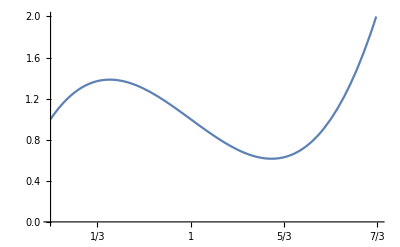

```mathematica
Plot[f[x],{x,0,2+1/3},PlotRange->{0,2},Ticks->{Range[1/3,2+1/3,1/3],Automatic},GridLines->{Range[1/3,2+1/3,1/3](*~Join~{extra vline}*),Automatic}]
```

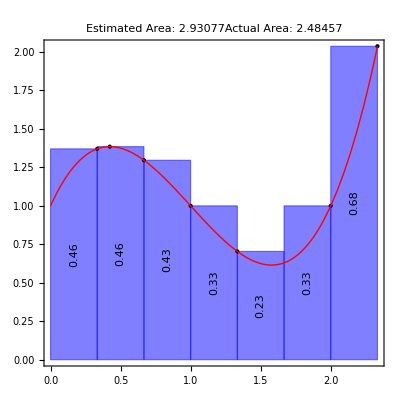

```mathematica
RiemannPlotPart[f[x],{x,0,2+1/3,Range[0,2+1/3,1/3],{1/3,1-1/(√3),2/3,1,4/3,2,7/3}}]
```

```mathematica
(*x*)
```

```mathematica
(*x*)
```

```mathematica
RiemannPlotPart[f[x],{x,0,2+1/3,Range[0,2+1/3,1/3],{1/3,1-1/(√3),2/3,1,1+1/3,2,2+1/3}}]
```

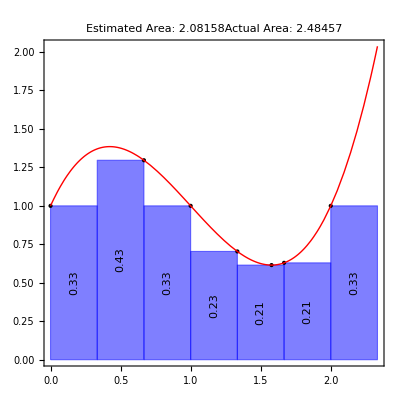

```mathematica
RiemannPlotPart[f[x],{x,0,2+1/3,Range[0,2+1/3,1/3],{0,2/3,1,1+1/3,1+1/(√3),1+2/3,2}}]
```

```mathematica
(*end class*)
```

```mathematica
RiemannPlot[Sin[x],{x,0,π,10},ExtentSize->Full]
```

```mathematica
RiemannPlot[Sin[x],{x,0,π,100},ExtentSize->Full]
```

```mathematica
RiemannPlot[2x+3,{x,1,4,3},ExtentSize->Right]
```

```mathematica
RiemannPlot[1-t,{t,0,3,6},ExtentSize->Right]
```

```mathematica
f[x_]:=1+2Sin[2x]
F[x_]:=Evaluate[Integrate[f[t],{t,0,x}]]
```

```mathematica
a=0; b=4;
Manipulate[
Row[{
Show[Plot[f[t],{t,a,b},
PlotLabel-> Row[{"x=",x,"  Area under graph: ",NumberForm[NIntegrate[f[t],{t,0,x}],{5,2}]}],
PlotRange->{-1.1,3.1}, ImageSize->Medium],
If[x>0,Plot[f[t],{t,a,x},Filling->0],{}]],
Show[Plot[F[x],{x,a,b},ImageSize->Medium, PlotLabel->"Accumulation Function"], Graphics[{PointSize[Large],Point[{x,F[x]}]}]]}]
,{{x,1},0,4},ControlPlacement->Top]
```

```mathematica
a=0; b=4;
Manipulate[
Show[Plot[f[t],{t,a,b},
PlotLabel-> Row[{"x=",x,"  h=",h,"  Orange Area: ",NumberForm[NIntegrate[f[t],{t,x,x+h}],3], "  Divided by h: ",NumberForm[NIntegrate[f[t],{t,x,x+h}]/h,{5,2}]}],
PlotRange->{-1.1,3.1}, ImageSize->Medium],
If[x>0,Plot[f[t],{t,a,x},Filling->0],{}],
Plot[f[t],{t,x,x+h},Filling->0, FillingStyle->Directive[Opacity[0.5],Orange]]]
,{{x,1},0,4},{{h,0.1},0.001,0.1},ControlPlacement->Top]
```

```mathematica
(*Class 13 -- Logarithms*)
```

```mathematica
Manipulate[
Show[Plot[1/t,{t,-3,10},
PlotLabel-> Row[{"x=",x,"  Value: ",If[x>0,NumberForm[Log[x],3],"?"]}],
PlotRange->{-1.1,3.1}, ImageSize->Medium],
If[x!=1,Plot[1/t,{t,1,x},Filling->0],{}],Graphics[Line[{{1,0},{1,1}}]]]
,{{x,1},-3,10},ControlPlacement->Top]
```

```mathematica
Plot[Log[t],{t,0,10},PlotLabel->"Graph of ln(x)"]
```

```mathematica
Plot[1/x,{x,-10,10}, PlotLabel->"Graph of 1/x"]
```

```mathematica
ln[x_]:=Evaluate[Piecewise[{{Integrate[1/t,{t,1,x}], x>0}, {Undefined, x<=0}}]]
Plot[ln'[x],{x,-10,10},PlotLabel->"Graph of ln'(x)", PlotRange -> {{-10,10},{-1,1}}]
```

```mathematica
f[x_]:=Piecewise[{{ln[x], x>0}, {ln[-x], x<0}}]
Plot[f[x]-1,{x,-10,10},PlotLabel->"Graph of ln|x|", PlotRange -> {{-10,10},{-1,4}}]
Plot[f'[x],{x,-10,10},PlotLabel->"Graph of ln'|x|", PlotRange -> {{-10,10},{-1,1}}]
```

```mathematica
f[x_]:=3+Piecewise[{{ln[x], x>0}, {ln[-x], x<0}}]
Plot[f[x],{x,-10,10},PlotLabel->"Graph of 3+ln|x|", PlotRange -> {{-10,10},{-1,5}}]
Plot[f'[x],{x,-10,10},PlotLabel->"Graph of its derivative", PlotRange -> {{-10,10},{-1,1}}]
```

```mathematica
f[x_]:=Piecewise[{{ln[x]-2, x>0}, {ln[-x]+1, x<0}}]
Plot[f[x],{x,-10,10},PlotLabel->"Graph of ln|x| with a different constant on each side", PlotRange -> {{-10,10},{-3,4}}]
Plot[f'[x],{x,-10,10},PlotLabel->"Graph of its derivative", PlotRange -> {{-10,10},{-1,1}}]
```

```mathematica
Plot[-ln[Cos[x]],{x,-6,12},PlotLabel->"-ln(cos(x))", PlotRange->{-1,4}]
```

```mathematica
Plot[-ln[Abs[Cos[x]]],{x,-6,12},PlotLabel->"-ln|cos(x)|", PlotRange->{-1,4}]
```

```mathematica
randomconstants =<||>
randomconstant[x_]:=If[KeyExistsQ[randomconstants,Floor[x/π+1/2]],randomconstants[Floor[x/π+1/2]],randomconstants[Floor[x/π+1/2]]=RandomReal[{-3,3}]]
f[x_]:=-ln[Abs[Cos[x]]]+randomconstant[x]
```

```mathematica
randomconstants=<||>
Plot[f[x],{x,-5,20},PlotLabel->"-ln|cos(x)| + many constants", PlotRange->{-4,4}]
```

```mathematica
Manipulate[
Show[Plot[Log[t],{t,0,10},
PlotLabel-> Row[{"x=",x,"  ln(x): ",If[x>0,NumberForm[Log[x],5],"?"]}],
PlotRange->{-1.1,3.1}, ImageSize->Medium],
Graphics[Line[{{x,0},{x,Log[x]}}]]]
,{{x,1},-3,10},ControlPlacement->Top]
```

```mathematica
Show[Plot[Exp[t],{t,-2,2}, Ticks->{Automatic, Range[7]}],
Graphics[{Line[{{0,E},{1,E}}],Line[{{1,0},{1,E}}]}]]
```